# STIRAP calculations

#### Simulations done in python, algebra done here

## Lvl 0 - Single 3-level atom, No S.E.

```mathematica
Clear["Global`*"]
H = ℏ{{0, -O1/2, 0},{-O1/2, -D1, -O2/2},{0, -O2/2, -(D1+D2)}};
```

```mathematica
H//MatrixForm
```

(0 | -(O1 ℏ)/2 | 0
-(O1 ℏ)/2 | -D1 ℏ | -(O2 ℏ)/2
0 | -(O2 ℏ)/2 | (-D1-D2) ℏ)

```mathematica
Table[Subscript[ρ, i,j],{i,1,3},{j,1,3}]
```

{{ρ_(1,1),ρ_(1,2),ρ_(1,3)},{ρ_(2,1),ρ_(2,2),ρ_(2,3)},{ρ_(3,1),ρ_(3,2),ρ_(3,3)}}

```mathematica
rho ={{Subscript[ρ, 1,1],Subscript[ρ, 1,2],Subscript[ρ, 1,3]},{Subscript[ρ, 1,2]*,Subscript[ρ, 2,2],Subscript[ρ, 2,3]},{Subscript[ρ, 1,3]*,Subscript[ρ, 2,3]*,Subscript[ρ, 3,3]}}
```

{{ρ_(1,1),ρ_(1,2),ρ_(1,3)},{Conjugate[ρ_(1,2)],ρ_(2,2),ρ_(2,3)},{Conjugate[ρ_(1,3)],Conjugate[ρ_(2,3)],ρ_(3,3)}}

```mathematica
rho//MatrixForm
```

(ρ_(1,1) | ρ_(1,2) | ρ_(1,3)
Conjugate[ρ_(1,2)] | ρ_(2,2) | ρ_(2,3)
Conjugate[ρ_(1,3)] | Conjugate[ρ_(2,3)] | ρ_(3,3))

```mathematica
({{Subscript[ρ, 1,1], Subscript[ρ, 1,2], Subscript[ρ, 1,3]}, {Subscript[ρ, 1,2]*, Subscript[ρ, 2,2], Subscript[ρ, 2,3]}, {Subscript[ρ, 1,3]*, ρ_(2,3*), Subscript[ρ, 3,3]}})
```

{{ρ_(1,1),ρ_(1,2),ρ_(1,3)},{Conjugate[ρ_(1,2)],ρ_(2,2),ρ_(2,3)},{Conjugate[ρ_(1,3)],ρ_(2,3),ρ_(3,3)}}

```mathematica
A = rho.H - H.rho//Simplify
```

{{1/2 O1 ℏ (Conjugate[ρ_(1,2)]-ρ_(1,2)),-1/2 ℏ (O1 ρ_(1,1)+2 D1 ρ_(1,2)+O2 ρ_(1,3)-O1 ρ_(2,2)),-1/2 ℏ (O2 ρ_(1,2)+2 (D1+D2) ρ_(1,3)-O1 ρ_(2,3))},{1/2 ℏ (2 D1 Conjugate[ρ_(1,2)]+O2 Conjugate[ρ_(1,3)]+O1 (ρ_(1,1)-ρ_(2,2))),1/2 ℏ (-O1 Conjugate[ρ_(1,2)]+O2 Conjugate[ρ_(2,3)]+O1 ρ_(1,2)-O2 ρ_(2,3)),1/2 ℏ (O1 ρ_(1,3)-O2 ρ_(2,2)-2 D2 ρ_(2,3)+O2 ρ_(3,3))},{1/2 ℏ (O2 Conjugate[ρ_(1,2)]+2 (D1+D2) Conjugate[ρ_(1,3)]-O1 Conjugate[ρ_(2,3)]),-1/2 ℏ (O1 Conjugate[ρ_(1,3)]-2 D2 Conjugate[ρ_(2,3)]+O2 (-ρ_(2,2)+ρ_(3,3))),1/2 O2 ℏ (-Conjugate[ρ_(2,3)]+ρ_(2,3))}}

Adiabatic pulses:  dθ/dt <<√(Ω_1^2+Ω_2^2)

```mathematica
Clear[dt,w]
Ω1[t_] := ⅇ^((-(t-dt/2)^2)/(2 w^2));Ω2[t_] := ⅇ^((-(t+dt/2)^2)/(2 w^2));θ[t_]:=ArcTan[Ω1[t]/Ω2[t]];
```

```mathematica
D[ArcTan[Ω1[t]/Ω2[t]],t]//Simplify
```

(dt ⅇ^((dt t)/w^2))/((1+ⅇ^((2 dt t)/w^2)) w^2)

```mathematica
Clear[dt]
Ωmax = 100;
Ωrms[t_, w_,dt_]:=Ωmax √(ⅇ^((-(t-dt/2)^2)/w^2)+ⅇ^((-(t+dt/2)^2)/w^2));
condition[t_,w_,dt_]:=Abs[(dt ⅇ^((dt t)/w^2))/((1+ⅇ^((2 dt t)/w^2)) w^2)]-Ωrms[t,w, dt]; (*want this << 0*)
condition2[t_,w_,dt_]:=w Ωrms[t,w, dt];(*want this >> 1*)
```

```mathematica
(*w = 5*)
dt = 20; (*on the order of the pi time for rabi frequencies = 2π *)
Manipulate[Plot[{-condition[t,w,dt],condition2[t,w,dt],50 ⅇ^((-(t-dt/2)^2)/(2 w^2)),50 ⅇ^((-(t+dt/2)^2)/(2 w^2))},{t,-50,50}, PlotRange->{0,100}],{w,1,100}]
```

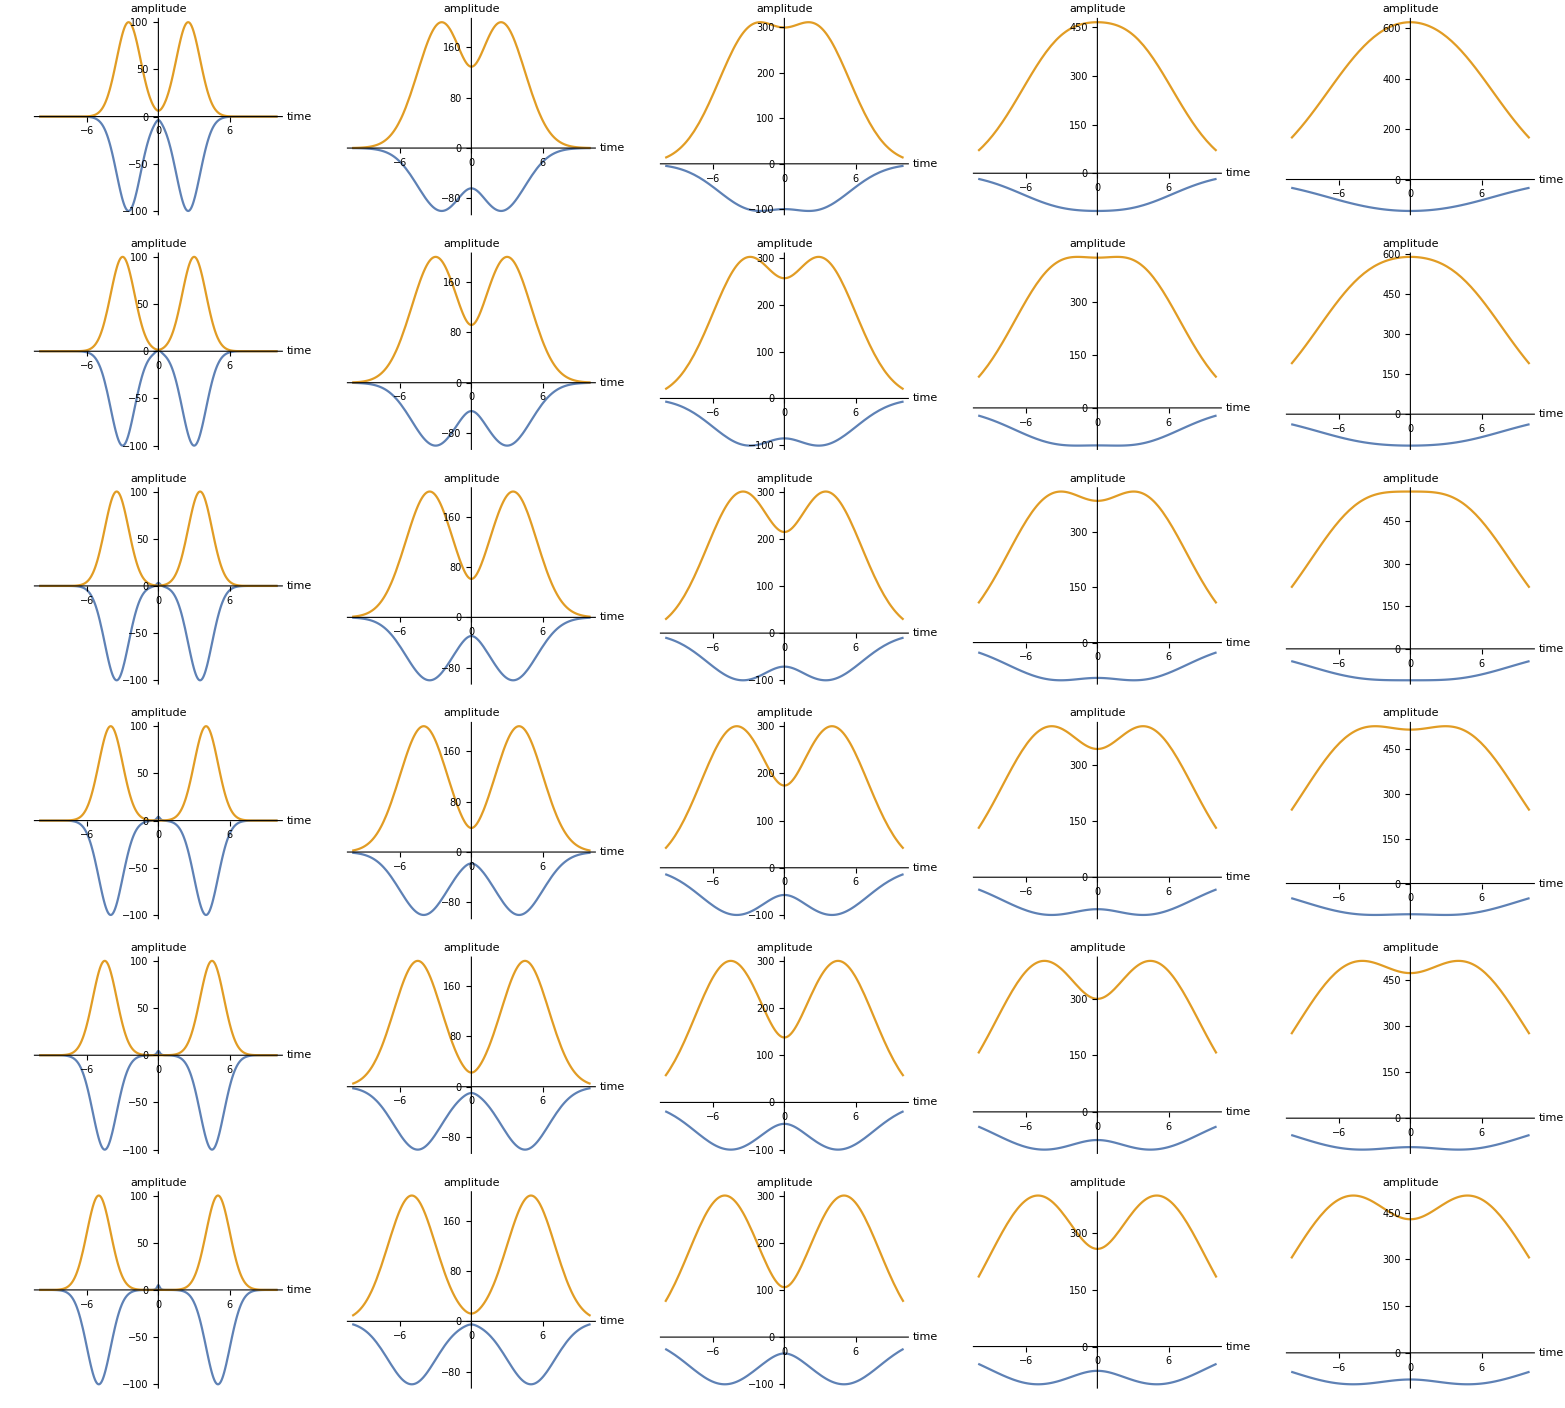

```mathematica
Grid[Table[Plot[{condition[t,w,dt],condition2[t,w,dt]},{t,-10,10},AxesLabel->{"time","amplitude"}],{dt,5,10},{w,1,5}]]
```

Want rms pulse area >> π/2, which is the integral of arctan(Ω1/Ω2) over time regardless of pulse structure.

```mathematica
Integrate[θ[t],{t,-20,20}]
```

$Aborted

```mathematica
Clear[w,dt]
Grid[√(Integrate[Ω1[t],{t,-∞,∞}]^2+Integrate[Ω2[t],{t,-∞,∞}]^2),{dt,5,10},{w,1,5}]
```

Grid[ConditionalExpression[2 √π √(w^2),Re[w^2]≥0],{dt,5,10},{w,1,5}]

rms pulse area is independent of spacing between the pulses, if I did this correctly. So choose w to give A_rms>> π/2, then try wider spacing

```mathematica
Solve[2 √π √(w^2)==π/2]
```

{{w→-(√π)/4},{w→(√π)/4}}

```mathematica
100* √π /4 //N
```

44.3113

```mathematica
Clear[dt,w]
Integrate[Ω1[t],{t,-∞,∞}]
```

ConditionalExpression[(√(2 π))/(√(1/w^2)),Re[w^2]≥0]

```mathematica
Solve[√(2 π)10*O==20π]
```

{{O→√(2 π)}}

```mathematica
√(2 π)/(2π)//N
```

0.398942

```mathematica
10 √(2 π)//N
```

25.0663

Turns out stirap works when you obey the conditions above, and make sure that the single photon detunings (defined wrt to the un-Stark-shifted state) are constant and opposite.

## Lvl 1 - Single 3-level atom w/ S.E.

```mathematica
H = ({{0, -Ω1/2, 0}, {-Ω1/2, -Δ1, -Ω2/2}, {0, -Ω2/2, -(Δ1+Δ2)}});
ρ = ({{Subscript[r, 1,1], Subscript[r, 1,2], Subscript[r, 1,3]}, {Subscript[r, 1,2]*, Subscript[r, 2,2], Subscript[r, 2,3]}, {Subscript[r, 1,3]*, Subscript[r, 2,3]*, Subscript[r, 3,3]}});
Γ = ({{γ11, 0, 0}, {0, γ22, 0}, {0, 0, γ33}});
```

```mathematica
dρ = ⅈ (ρ.H - H.ρ) -1/2(Γ.ρ + ρ.Γ);
```

```mathematica
For[j = 1, j< 4, j++,
For[i = 1, i<j+1, i++,
Print[{i,j,dρ[[i]][[j]]}]
]
]
```

{1,1,-γ11 r_(1,1)+ⅈ (1/2 Ω1 Conjugate[r_(1,2)]-1/2 Ω1 r_(1,2))}

{1,2,1/2 (-γ11 r_(1,2)-γ22 r_(1,2))+ⅈ (-1/2 Ω1 r_(1,1)-Δ1 r_(1,2)-1/2 Ω2 r_(1,3)+1/2 Ω1 r_(2,2))}

{2,2,-γ22 r_(2,2)+ⅈ (-1/2 Ω1 Conjugate[r_(1,2)]+1/2 Ω2 Conjugate[r_(2,3)]+1/2 Ω1 r_(1,2)-1/2 Ω2 r_(2,3))}

{1,3,1/2 (-γ11 r_(1,3)-γ33 r_(1,3))+ⅈ (-1/2 Ω2 r_(1,2)+(-Δ1-Δ2) r_(1,3)+1/2 Ω1 r_(2,3))}

{2,3,1/2 (-γ22 r_(2,3)-γ33 r_(2,3))+ⅈ (1/2 Ω1 r_(1,3)-1/2 Ω2 r_(2,2)+Δ1 r_(2,3)+(-Δ1-Δ2) r_(2,3)+1/2 Ω2 r_(3,3))}

{3,3,ⅈ (-1/2 Ω2 Conjugate[r_(2,3)]+1/2 Ω2 r_(2,3))-γ33 r_(3,3)}